```mathematica
Загружаем результаты из файла
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=Import["gradDescWithSpalStep.dat"];
points=data[[All,{1,2}]];
fValues=data[[All,3]];
κArray =data[[All,4]];
norm=data[[All,5]];
len=Length[norm];
```

```mathematica
Определяем необходимые функции
```

```mathematica
α=1;
```

```mathematica
f[{x_,y_}]:=α(x^2-y)^2+(x-1)^2
```

```mathematica
АНАЛИЗ РЕЗУЛЬТАТОВ ВЫЧИСЛИТЕЛЬНОГО ЭКСПЕРИМЕНТА
```

```mathematica
1. Траектория поиска точки минимума
```

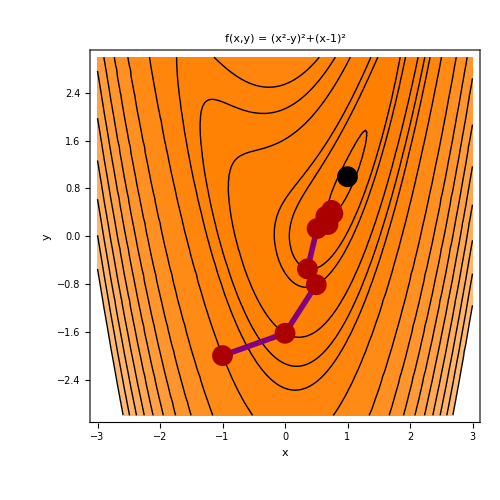

```mathematica
CP0={-3,-3};num=9;
ContourPlot[f[{x,y}],{x,CP0[[1]],3},{y,CP0[[2]],3},Contours->uniformMesh[fValues[[1]],0.8(f[CP0]-fValues[[1]]),10]~Join~uniformMesh[fValues[[2]],0.8(fValues[[1]]-fValues[[2]]),2]~Join~fValues[[1;;4]]~Join~{fValues[[8]],fValues[[20]]},ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",f[{x,y}]}],Large],LabelStyle->Large,FrameStyle->Thick,ImageSize->500,Epilog->{Purple,Thickness[0.008],Table[Arrow[points[[i-1;;i]]],{i,2,num}],Darker[Red],PointSize[0.03],Point[points[[1;;num]]],Black,Point[points[[len]]]}]
```

```mathematica
2. Анализ сходимости метода: убывание нормы невязки
```

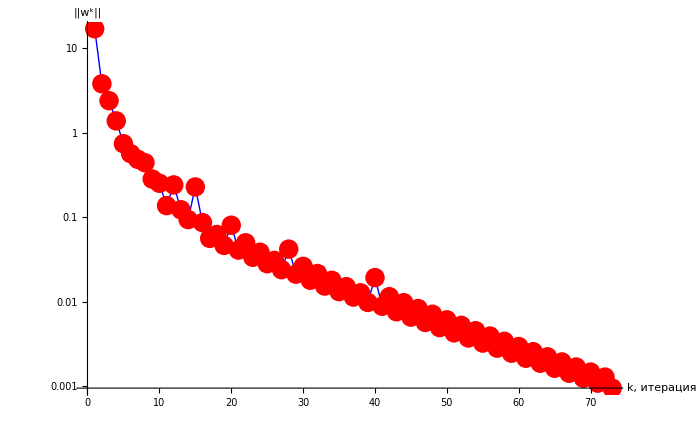

```mathematica
ListLogPlot[norm,PlotRange->All,PlotStyle->{Blue,Thick,PointSize[Large]},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k, итерация","||w^k||"},ImageSize->700,Joined->True,Mesh->Full,MeshStyle->Directive[PointSize[0.02],Red]]
```

```mathematica
3. Таблицы
```

```mathematica
gridLabel={"k","X^k","f(X^k)","κ_k","||w^k||"};gridData=Table[Table[{},{j,1,Length[gridLabel]}],{i,1,len}];gridData[[All,1]]=Table[i,{i,0,len-1}];
For[i=1,i≤len,i++,gridData[[i,2]]="( "<>ToString[SetAccuracy[points[[i,1]],8]]<>", "<>ToString[SetAccuracy[points[[i,2]],8]]<>" )"]
gridData[[All,3]]=SetAccuracy[fValues,8];
gridData[[All,4]]=SetAccuracy[κArray,8];
gridData[[All,5]]=SetAccuracy[norm,8];
gridData={gridLabel}~Join~gridData;
```

```mathematica
Grid[gridData[[1;;10]]~Join~{Table["...",{i,1,Length[gridLabel]}]}~Join~gridData[[len-4;;len+1]],Frame->All,FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15]]
```

k | X^k | f(X^k) | κ_k | ||w^k||
0 | ( -1.0000000, -2.0000000 ) | 13. | 1. | 17.088
1 | (      -8
0. 10, -1.6250000 ) | 3.64063 | 0.0625 | 3.81608
2 | ( 0.5000000, -0.8125000 ) | 1.37891 | 0.25 | 2.40442
3 | ( 0.3593750, -0.5468750 ) | 0.867411 | 0.125 | 1.38701
4 | ( 0.5141070, 0.1291500 ) | 0.254359 | 0.5 | 0.744644
5 | ( 0.6875690, 0.1967280 ) | 0.173802 | 0.25 | 0.568142
6 | ( 0.6540000, 0.3347400 ) | 0.128361 | 0.25 | 0.485776
7 | ( 0.7661940, 0.3812280 ) | 0.0970294 | 0.25 | 0.442819
8 | ( 0.7457940, 0.4326840 ) | 0.079879 | 0.125 | 0.283919
... | ... | ... | ... | ...
67 | ( 0.9986060, 0.9969110 ) | 2.×10^-6 | 0.25 | 0.0016866
68 | ( 0.9988030, 0.9969870 ) | 1.8×10^-6 | 0.125 | 0.0012444
69 | ( 0.9987820, 0.9972970 ) | 1.6×10^-6 | 0.25 | 0.0014695
70 | ( 0.9989530, 0.9973640 ) | 1.4×10^-6 | 0.125 | 0.001087
71 | ( 0.9989350, 0.9976350 ) | 1.2×10^-6 | 0.25 | 0.001281
72 | ( 0.9990840, 0.9976940 ) | 1.1×10^-6 | 0.125 | 0.0009497